### Categorization

Tutorial

EcoEvo Package

EcoEvo`

EcoEvo/tutorial/Trait-BasedLotka-VolterraCompetition

### Keywords

### Syntax Templates

Details

# Trait-Based Lotka-Volterra Competition

The trait-based Lotka-Volterra competition model considers competing species (n_i) with a single trait (x_i) that determines carrying capacity and the strength of competition.  It is the canonical example used in adaptive dynamics.

k[x_i] describes the trait-dependence of the carrying capacity and a[x_i,x_j] describes how the strength of competition depends on the difference between species traits.  Typically we assume that k[x_i] is unimodal and a[x_i,x_j] is a symmetric function of x_i-x_j and declines as the trait difference increases.  For example,

```mathematica
Needs["EcoEvo`"];
```

Set up model:

```mathematica
SetModel[{
Guild[n]->{Variable->n,Equation->g,Trait[x]->{Range->Interval[{-1,1}]}}
}]
```

```mathematica
g[i_]:=(k[Subscript[x, i]]-Sum[a[Subscript[x, i],Subscript[x, j]]*Subscript[n, j][t],{j,Subscript[𝒩, n]}])*Subscript[n, i][t];
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σ^2);
k[x_]:=1-x^2;
```

Plot density-independent growth rate and competition kernel:

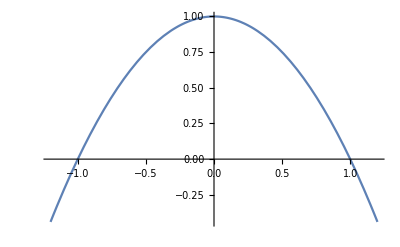

```mathematica
Plot[k[x],{x,-1.2,1.2}]
```

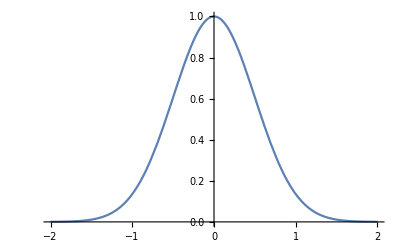

```mathematica
σ=1/2;
Plot[a[x,0],{x,-2,2}]
```

Let's start with some analytical work.

```mathematica
Clear[σ]
```

Find the one-species ecological equilibria, then solve for one-species evolutionary equilibria:

```mathematica
eq1=SolveEcoEq[{Subscript[𝒩, n]->1}]⟦-1⟧
evoeq=SolveEvoEq[eq1]
```

{n_1→1-x_1^2}

{{x_1→0}}

Now check convergence stability with EvoEigenvalues:

```mathematica
EvoEigenvalues[evoeq⟦1⟧,eq1]
```

{-2}

Negative EvoEigenvalues indicates convergence stability.

Checking (local) evolutionary stability by taking the second derivative with DInv:

```mathematica
DInv[evoeq⟦1⟧,eq1,{Subscript[x, 0],2}]
```

{-2+1/σ^2}

The border between ESS and non-ESS:

```mathematica
Solve[DInv[evoeq⟦1⟧,eq1,{Subscript[x, 0],2}]==0,σ]
```

{{σ→-1/(√2)},{σ→1/(√2)}}

The {x_1→0} evolutionary equilibrium is always convergence stable and evolutionarily stable whenever σ>1/√2=0.707107.

Now let's set σ=0.5 and proceed with numerical analysis.

```mathematica
σ=0.5;
```

Simulate the ecological dynamics of a single species:

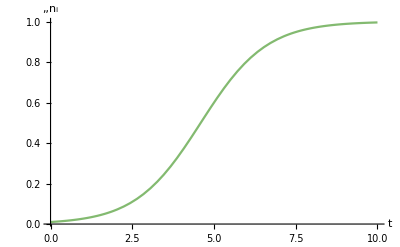

```mathematica
sol=EcoSim[{Subscript[x, 1]->0},{Subscript[n, 1]->0.01},10];
PlotDynamics[sol]
```

Pairwise competition:

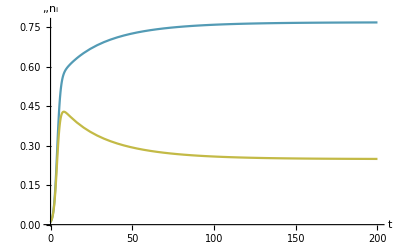

```mathematica
traits={Subscript[x, 1]->0,Subscript[x, 2]->0.2};
sol=EcoSim[traits,{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01},200];
PlotDynamics[sol]
```

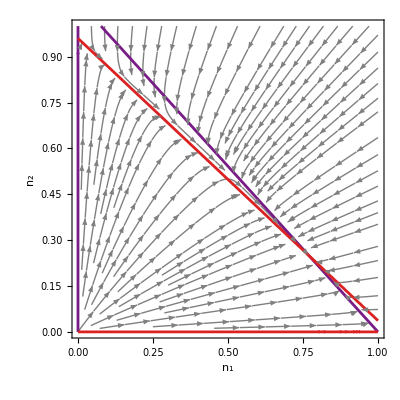

```mathematica
PlotEcoPhasePlane[traits,{Subscript[n, 1],0,1},{Subscript[n, 2],0,1}]
```

Competition among 101 number of species evenly spaced along the trait axis.

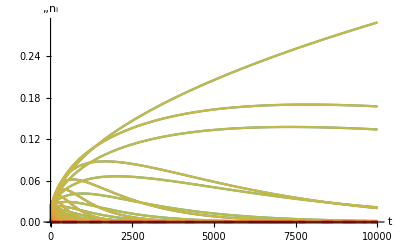

```mathematica
traits=MakeRuleList[x,101,{-1,1}];
ics=MakeRuleList[n,101,0.001];
sol=EcoSim[traits,ics,10^4];
PlotDynamics[sol]
```

We can get another view on the outcome by plotting a trait-abundance distribution with PlotTAD:

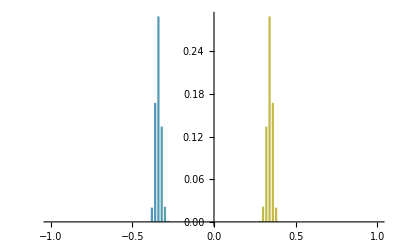

```mathematica
PlotTAD[traits,FinalSlice[sol]]
```

The community reduces to two clusters of similar species at t=10^4.  Let's analyze using adaptive dynamics, starting with a pairwise invasibility plot (PIP).  Using the one-species ecological equilibrium eq1  speeds calculations:

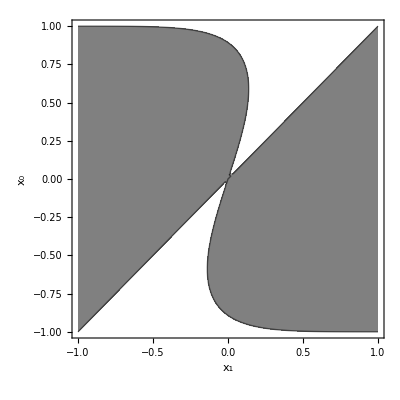

```mathematica
PlotPIP[eq1,{Subscript[x, 1],-1,1}]
```

Looks like a branching point at x=0.  To verify this, start by finding the eco-evo equilibrium:

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[n, 1]->0.9}]
```

{n_1→1.,x_1→0}

Take a look at the fitness landscape at the eco-evo equilibrium:

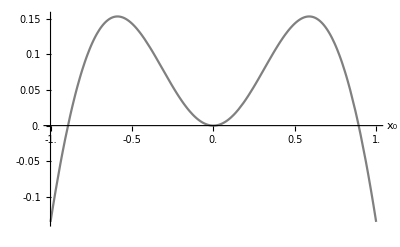

```mathematica
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

We can check evolutionary stability locally with DInv and globally with GlobalESSQ.

```mathematica
DInv[eq,{Subscript[x, 0],2}]
```

{2.}

The second derivative of fitness with respect to the invader is positive, indicating a non-ESS.  GlobalESSQ agrees:

```mathematica
GlobalESSQ[eq]
```

{{False},{{0.153426,{x→-0.588705}}}}

We can check convergence stability with EvoEigenvalues:

```mathematica
EvoEigenvalues[eq]
```

{-2}

The negative EvoEigenvalues indicate convergence stability.  Taken together with the non-ESS finding, this is an evolutionary branching point.  We can simulate the branching using EcoEvoSim, starting with two similar species far from the branching point and small genetic variance:

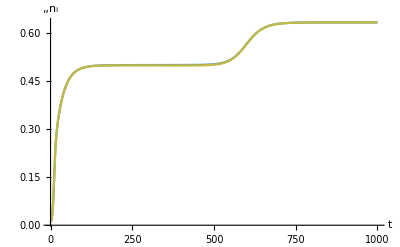

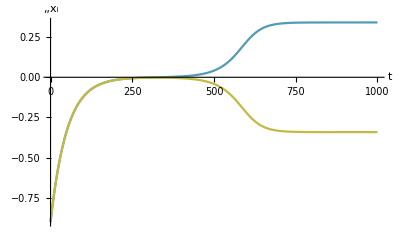

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->-0.9,Subscript[x, 2]->-0.90001},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01},{V[x]->0.01},1000];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

Take the final slice and plot the corresponding fitness landscape.

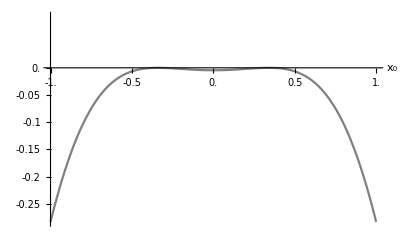

```mathematica
PlotInv[FinalSlice[sol],{Subscript[x, 0],-1,1}]
```

Another graphical approach is the evolutionary phase plane, which combines PlotMIP, PlotEvoStreams and  PlotEvoIsoclines.  Here we use analytical one- and two-species ecological equilibria to speed it up.

```mathematica
eq2=SolveEcoEq[{Subscript[𝒩, n]->2}]⟦-1⟧;
PlotEvoPhasePlane[eq1,eq2,{Subscript[x, 1],-1,1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics-

Use FindEcoEvoEq to get the eco-evolutionary equilibrium:

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5}]
```

{n_1→0.63373,n_2→0.63373,x_1→-0.340984,x_2→0.340984}

Verify that it's convergence stable and a global ESS.

```mathematica
EvoEigenvalues[eq]
```

{-3.72065,-2.}

```mathematica
GlobalESSQ[eq]
```

{{True},{{0.,{x→0.340984}}}}

Decreasing σ shows the loss of global evolutionary stability, which typically happens before the loss of local evolutionary stability.

```mathematica
σ=0.45;
```

{n_1→0.67552,n_2→0.67552,x_1→-0.349257,x_2→0.349257}

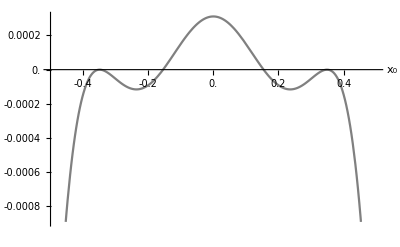

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5}]
PlotInv[eq,{Subscript[x, 0],-0.5,0.5}]
```

```mathematica
GlobalESSQ[eq]
```

{{False},{{0.000311214,{x→5.42199×10^-9}}}}

A three-species ESC replaces it, which we can find with FindEcoEvoEq and an carefully chosen guess.

```mathematica
eq3=FindEcoEvoEq[Join[eq,{Subscript[x, 3]->0,Subscript[n, 3]->0.01}]]
```

{n_1→0.658007,n_2→0.658007,n_3→0.0363144,x_1→-0.355242,x_2→0.355242,x_3→0}

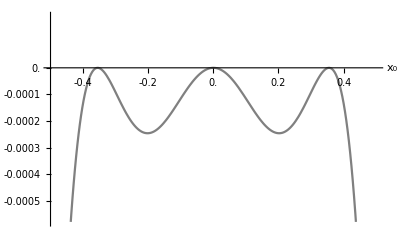

```mathematica
PlotInv[eq3,{Subscript[x, 0],-0.5,0.5}]
```

Verify evolutionary and convergence stability:

```mathematica
GlobalESSQ[eq3]
```

{{True},{{1.11022×10^-16,{x→-8.21604×10^-9}}}}

```mathematica
EvoEigenvalues[eq3]
```

{-4.74005,-2.,-0.157326}

### References

More About

Related Tutorials

ExampleModels

Related Wolfram Education Group Courses